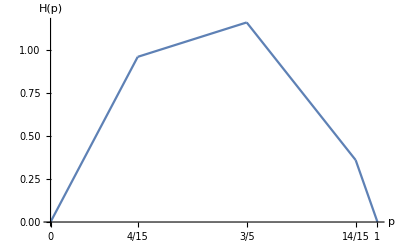

```mathematica
alpha=1/5;
mPar = 3;
hL[k_,m_,a_]:=k*(k+1)/2 - k*a
hH[k_,m_,b_]:=(m-k)*(m-k+1)/2 - (m-k)*b
omega[k_,m_,p_,a_]:=p*hH[k,m,1-a]+(1-p)*hL[k,m,a]
omegaMin[p_]:=Min[omega[#,mPar,p,alpha]& /@ Range[0,mPar]]
extremePoints = Table[
{(k+(1-alpha))/mPar, NumberForm[(k+(1-alpha))/mPar,2]},
{k, 0, mPar-1}
]~Join~{{0,0},{1,1}};
Plot[
omegaMin[p], {p,0,1},
PlotPoints->500, 
GridLines->{#[[1]]&/@extremePoints,Automatic}, GridLinesStyle->Dashed,
Ticks->{extremePoints, Automatic},
AxesLabel->{p, H[p]},
PlotLegends->Placed[
StringForm["m=``, α=``, β=``, β/m=``", mPar, alpha, 1-alpha, (1-alpha)/mPar],
Above
]
]
```

```mathematica
peak[k_,m_,a_] :=Simplify[omega[k,m,(k+1-a)/m,a]]
peak[k,m,a]
peak[0,m,a]
peak[m-1,m,a]
```

1/2 (-2 a^2-(1+k) (1+k-m)+a (3+2 k-m))

-1/2 (-1+a) (-1+2 a+m)

-1/2 a (-1+2 a-m)

```mathematica
Clear[lb,k,a,m]
RSolve[{
lb[k]==1/2+1/2*(lb[k-1]+lb[k+1]),
lb[0]==-1/2 (-1+a) (-1+2 a+m),
lb[m-1]==-1/2 a (-1+2 a-m)
},
lb[k],k
]
```

{{lb[k]→1/2 (-1+3 a-2 a^2-2 k+2 a k-k^2+m-a m+k m)}}

```mathematica
Simplify[1/2 (-1+3 a-2 a^2-2 k+2 a k-k^2+m-a m+k m)]
```

1/2 (-2 a^2-(1+k) (1+k-m)+a (3+2 k-m))